```mathematica
ClearAll
Clear[β1,β2,δ2,γ,ϵL1,ϵL2,ϵLA1,ϵLA2, p1,p2, S, V,R,n,ϵa,α,r,λ,δ1]

K=((p1*β1)/(δ1+γ))+((1-p1)*β2/(γ)) + ((((1-ϵl1)*(1-ϵa)*α*r)/(α*λ+α*(1-ϵa)*r+λ*(1-ϵa)*r))+(((1-ϵl2)*(1-ϵa)*λ*r)/(α*λ+α*(1-ϵa)*r+λ*(1-ϵa)*r)))*((p2*β1)/(δ2+γ)) + ((((1-ϵlA1)*(1-ϵa)*α*r)/(α*λ+α*(1-ϵa)*r+λ*(1-ϵa)*r))+(((1-ϵlA2)*(1-ϵa)*λ*r)/(α*λ+α*(1-ϵa)*r+λ*(1-ϵa)*r)))*(((1-p2)*β2)/(γ))
```

ClearAll

((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ

```mathematica
R=D[K,β1]*(β1/K)
W=D[K,β2]*(β2/K)
U=D[K,δ2]*(δ2/K)
P=D[K,δ1]*(δ1/K)
H=D[K,γ]*(γ/K)
T=D[K,p1]*(p1/K)
Q=D[K,p2]*(p2/K)
Y=D[K,ϵl1]*(ϵl1/K)
A=D[K,ϵl2]*(ϵl2/K)
F=D[K,ϵlA1]*(ϵlA1/K)
J=D[K,ϵlA2]*(ϵlA2/K)
L=D[K,ϵa]*(ϵa/K)
Z=D[K,r]*(r/K)
X=D[K,α]*(α/K)
B=D[K,λ]*(λ/K)
```

(β1 (p1/(γ+δ1)+(p2 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

(β2 ((1-p1)/γ+((1-p2) ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

-(p2 β1 δ2 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/((γ+δ2)^2 (((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ))

-(p1 β1 δ1)/((γ+δ1)^2 (((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ))

(γ (-((1-p1) β2)/γ^2-(p1 β1)/(γ+δ1)^2-(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)^2-((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ^2))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

(p1 (-β2/γ+β1/(γ+δ1)))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

(p2 ((β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)-(β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

General::ivar: 0.35 is not a valid variable.

(0.35 ∂_0.35 (((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

General::ivar: 0.59 is not a valid variable.

(0.59 ∂_0.59 (((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

General::ivar: 0.3 is not a valid variable.

(0.3 ∂_0.3 (((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

General::ivar: 0.49 is not a valid variable.

(0.49 ∂_0.49 (((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

(ϵa (((1-p2) β2 (-(0.7 r α (1-ϵa) (-r α-r λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2-(0.51 r (1-ϵa) λ (-r α-r λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2-(0.7 r α)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)-(0.51 r λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ+(p2 β1 (-(0.65 r α (1-ϵa) (-r α-r λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2-(0.41 r (1-ϵa) λ (-r α-r λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2-(0.65 r α)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)-(0.41 r λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

(r ((p2 β1 (-(0.65 r α (1-ϵa) (α (1-ϵa)+(1-ϵa) λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2-(0.41 r (1-ϵa) λ (α (1-ϵa)+(1-ϵa) λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2+(0.65 α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 (-(0.7 r α (1-ϵa) (α (1-ϵa)+(1-ϵa) λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2-(0.51 r (1-ϵa) λ (α (1-ϵa)+(1-ϵa) λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2+(0.7 α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

(α ((p2 β1 (-(0.65 r α (1-ϵa) (r (1-ϵa)+λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2-(0.41 r (1-ϵa) λ (r (1-ϵa)+λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2+(0.65 r (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 (-(0.7 r α (1-ϵa) (r (1-ϵa)+λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2-(0.51 r (1-ϵa) λ (r (1-ϵa)+λ))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2+(0.7 r (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

(λ ((p2 β1 (-(0.65 r α (α+r (1-ϵa)) (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2-(0.41 r (α+r (1-ϵa)) (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2+(0.41 r (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 (-(0.7 r α (α+r (1-ϵa)) (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2-(0.51 r (α+r (1-ϵa)) (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)^2+(0.51 r (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ))/(((1-p1) β2)/γ+(p1 β1)/(γ+δ1)+(p2 β1 ((0.65 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.41 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/(γ+δ2)+((1-p2) β2 ((0.7 r α (1-ϵa))/(r α (1-ϵa)+α λ+r (1-ϵa) λ)+(0.51 r (1-ϵa) λ)/(r α (1-ϵa)+α λ+r (1-ϵa) λ)))/γ)

```mathematica
β1=0.5
β2=0.08
δ1=0.00018256
δ2=0.000018256
γ=0.037
p1=0.12
ϵl1=0.35
ϵa=0.0862
ϵl2=0.59
ϵlA1=0.3
ϵlA2=0.49
α=0.05555
r=0.030421
p2=0.09
λ=0.0476
R
```

0.5

0.08

0.00018256

0.000018256

0.037

0.12

0.35

0.0862

0.59

0.3

0.49

0.05555

0.030421

0.09

0.0476

0.435908

```mathematica
W
```

0.564092

```mathematica
H
```

-0.998196

```mathematica
U
```

-0.0000375065

```mathematica
T
```

0.301994

```mathematica
Y
```

-0.0265834

```mathematica
L
```

-0.00976748

```mathematica
X
```

-0.0285915

```mathematica
Z
```

```mathematica
0.10354440001638786
Q
A
J
F
B
P
```

0.103544

0.0622288

General::ivar: 0.59 is not a valid variable.

0.131573 ∂_0.59 4.48419

General::ivar: 0.49 is not a valid variable.

0.109273 ∂_0.49 4.48419

General::ivar: 0.3 is not a valid variable.

0.0669017 ∂_0.3 4.48419

-0.0749529

-0.00176683

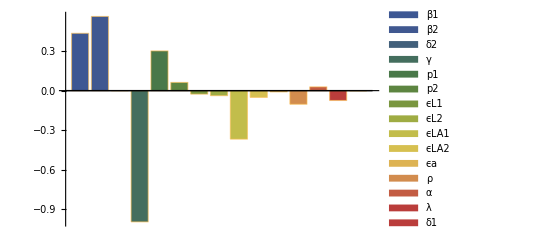

```mathematica
BarChart[{0.4359,0.5640,-0.0000375,-0.9981,0.30199,0.06222,-0.02658,-0.03839,-0.3688,-0.05161,-0.00976,-0.10354,0.0285,-0.07495,-0.0017},ChartLegends->{"β1","β2","δ2","γ","p1","p2","ϵL1","ϵL2","ϵLA1","ϵLA2","ϵa","ρ","α","λ","δ1"}, ChartStyle->"DarkRainbow"]
```